```mathematica
<<mf22.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];
Return[collect2]]
```

```mathematica
fLambda2[n_,m_]:=
Module[{jay,djay,numerator,denominator,answer},
jay=jNew[n+1,m]; (* n+1 instead of n avoids erros in highest order term. Why? *)
djay=x*D[jay,x];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-2^6*m^3);
answer=Collect[Series[(numerator/denominator)^(1/(m-2)),{x,0,n}],x];
Return[answer]]
```

```mathematica
rationalQ[x_]:=
IntegerQ[Numerator[x]]&&IntegerQ[Denominator[x]]&&!(Denominator[x]==0);
Attributes[rationalQ]=Listable
```

Listable

```mathematica
polyIsConstant[polynomial_]:=Module[{tf,degree},
tf=False;
degree=Exponent[poly,x];
If[degree==0,tf=True];
Return[tf]]
```

```mathematica
stream=OpenWrite["run6sept20no1"];
start=SessionTime[];
For[m=2,m<302,m++;
expansion=fLambda2[101,m];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 9824.2161

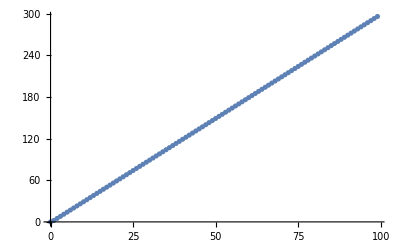

run14sept20no3

```mathematica
stream=OpenRead["run6sept20no1"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run14sept20no3"];
degrees={};
For[n=-1,n<99,n++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Expand[ip];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run14sept20no3"];
list=ReadList[stream];
Close[stream];
yes=0;
For[k=0,k<100,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
test=(n==0)&&(poly/.x->0)==1&&polyIsConstant[poly];
If[test,Print[poly]]]
```

1